```mathematica
f[x_] = Log[0.31*x] - 1.3*x +2.5
```

2.5-1.3 x+Log[0.31 x]

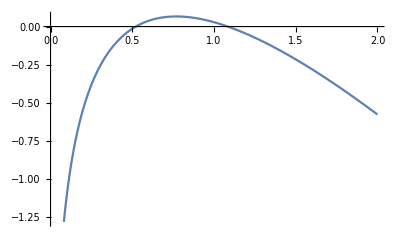

```mathematica
Plot[f[x],{x,0,2}]
```

```mathematica
FindRoot[f[x],{x,0.1}]
```

{x→0.52179}

```mathematica
FindRoot[f[x],{x,1}]
```

{x→1.08473}

```mathematica
f1[x_] = f'[x]
```

-1.3+1./x

```mathematica
f2[x_] = f''[x]
```

-1./x^2